```mathematica
Needs["NeffConstraint`"]
```

### Analyze Cosmology of aDM between recombination and annihilation

```mathematica
CosmoParams[]
```

{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}

#### Initialize

```mathematica
inter1me=InterpolateEtransRate[me,me,1];
inter2000me=InterpolateEtransRate[2000 me,me,1];
testΔEdict =InterpolateTotEtrans[{ ("me"/.CosmoParams[])10^-9,("me"/.CosmoParams[])10^4 },("me"/.CosmoParams[]),1,CosmoParams[]];
```

$Aborted

#### Plot hubble and aH

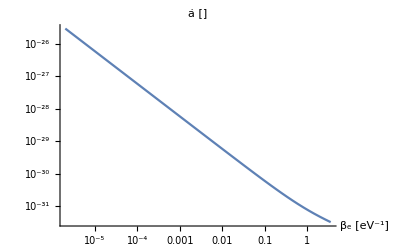

```mathematica
LogLogPlot[aH[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"ȧ []",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

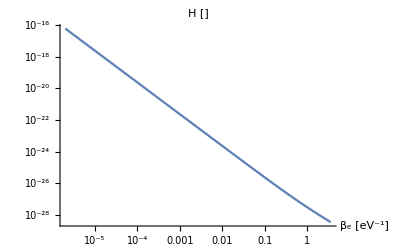

```mathematica
LogLogPlot[H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"H []",AxesLabel->{"β_e [eV^-1]"},PlotRange->All]
```

#### Screening length comparison and Expected rate scaling

Λ and 1/(Z_1 β ȧ) control the scaling of the rate

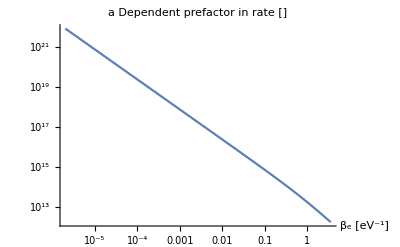

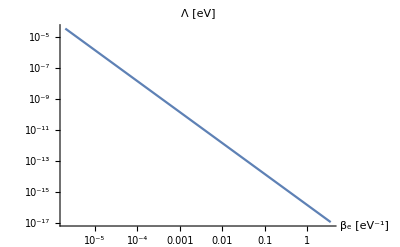

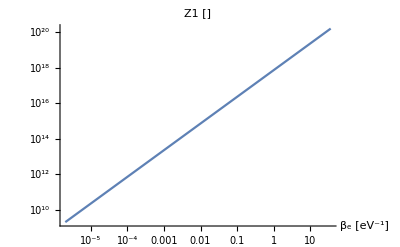

```mathematica
LogLogPlot[1/(Z1[β] aH[β]β)/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"a Dependent prefactor in rate []",AxesLabel->{"β_e [eV^-1]"}]
LogLogPlot[Λ[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Λ [eV]",AxesLabel->{"β_e [eV^-1]"}]
LogLogPlot[Z1[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],10/("TR")/.CosmoParams[]},PlotLabel->"Z1 []",AxesLabel->{"β_e [eV^-1]"}]
```

So it seems like partition function dominates over temperature scaling of a, and the reduced screening at late times.

```mathematica
Z1[1/("Td")]/.CosmoParams[]
```

2.00913×10^9

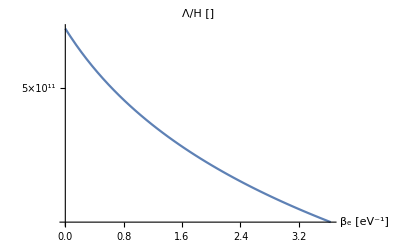

```mathematica
LogPlot[Λ[β]/H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"Λ/H []",AxesLabel->{"β_e [eV^-1]"}]
```

Screening length (Debeye momentum) - minimum momentum transfered

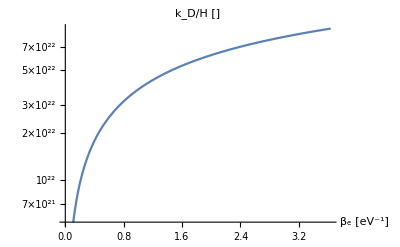

```mathematica
LogPlot[(√(2 "me" Λ[β]))/H[β]/.CosmoParams[],{β,1/("Td")/.CosmoParams[],1/("TR")/.CosmoParams[]},PlotLabel->"k_D/H []",AxesLabel->{"β_e [eV^-1]"}]
```

#### Rate and Energy plots - SM aDM mass values

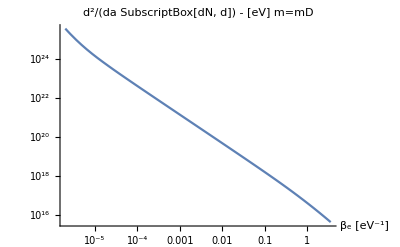

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[β me]],{β,1/Td,1/TR},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"β_e [eV^-1]"}]
```

m=mD

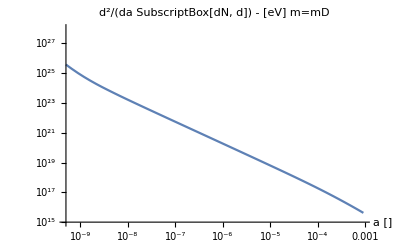

```mathematica
LogLogPlot[10^inter1me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] m=mD",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

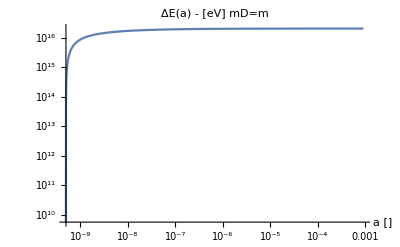

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter1me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=m",AxesLabel->{"a []"},PlotRange->All]
```

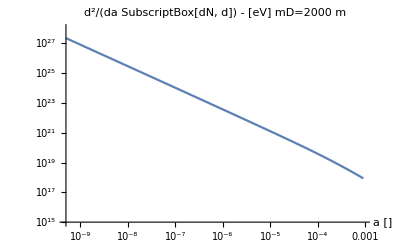

```mathematica
LogLogPlot[10^inter2000me[["f"]][Log10[a/Tdt me]],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"d^2/(da SubscriptBox[dN, d]) - [eV] mD=2000 m",AxesLabel->{"a []"},PlotRange->{10^15,10^28}]
```

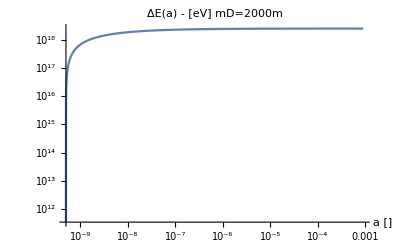

```mathematica
LogLogPlot[NIntegrate[Tdt 10^inter2000me[["f"]][Log10[β me]],{β,1/Td,a/Tdt}],{a,(Tdt/Td),(Tdt/TR)},PlotLabel->"ΔE(a) - [eV] mD=2000m",AxesLabel->{"a []"},PlotRange->All]
```

#### Neff constraint

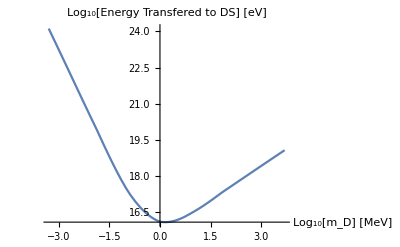

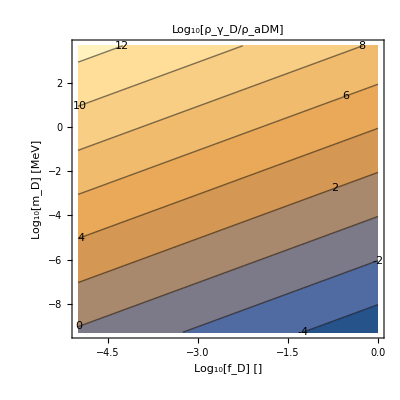

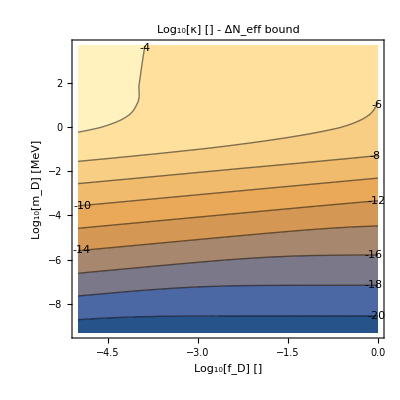

```mathematica
ComputeΔNeffConstraint[testΔEdict]
```

#### Interaction Rate - IR domination Debugging

```mathematica
(*NumIntegrand[mDt_,mt_,κ_,ξβ_?NumberQ,ξE_?NumberQ,params_,l_:1]:= Module[{Integrand},
(*l - == 1 => energy transfer rate integrand, == 0 => interaction rate (over Subscript[n, D]) integrand*)
 Integrate[Ett^l/(Ett+"Λ")^2 (("ms" + "ESMt")^2+("ms"+(Ett-"ESMt"))^2),Ett];
	Simplify[%/."ms"->("m"^2+"mD"^2)/(2 "mD")];
	Integrand =Simplify[Simplify[(%/.Ett->(2 "mD")/(("ESMt"+"mD")^2/("ESMt"^2-"m"^2)-1))-(%/.Ett->0)]];
2/π ("α"^2 κ^2)/mDt (E^(-"β" "ESMt" + "β" "μ")/aH["β"]^l Integrand /."μ"->"m" - 1/"β" Log["Qt"]/.{"Λ"->Λ["β"],"Qt"->Z1["β"]}/."ESMt"->1/"β" ξE + "m"/."β"->ξβ/"m"/.{"m"->mt,"mD"->mDt})/.params
]*)
```

```mathematica
(*ESMIntegral[mD_,m_,κ_,ξβ_?NumberQ,params_]:=(m/.params)/ξβ NIntegrate[ NumIntegrand[mD,m,κ,ξβ,ξE,params],{ξE,0,∞}](*extra factor comes from jacobian*)*)
```

```mathematica
inter1me=InterpolateEtransRate[("me"/.CosmoParams[]),("me"/.CosmoParams[]),1,CosmoParams[]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

<|f→InterpolatingFunction[…],ΔEtot→2.07738×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5858},{0.481511,24.5599},{0.963021,23.7462},{1.44453,23.0086},{1.92604,22.294},{2.40755,21.586},{2.88906,20.8797},{3.37057,20.1731},{3.85208,19.4649},{4.3336,18.7528},{4.81511,18.0304},{5.29662,17.2824},{5.77813,16.4843},{6.25964,15.6223}},mD→500000,m→500000,κ→1,params→{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}|>

```mathematica
interrate1me=InterpolateEtransRate[("me"/.CosmoParams[]),("me"/.CosmoParams[]),1,CosmoParams[],0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in NeffConstraint`Private`β near {NeffConstraint`Private`β} = {0.0000159974}. NIntegrate obtained 2.07738×10^16 and 3.80047×10^12 for the integral and error estimates.

<|f→InterpolatingFunction[…],ΔEtot→2.07738×10^16,ξβ→{0.,0.481511,0.963021,1.44453,1.92604,2.40755,2.88906,3.37057,3.85208,4.3336,4.81511,5.29662,5.77813,6.25964},Points→{{0.,25.5858},{0.481511,24.5599},{0.963021,23.7462},{1.44453,23.0086},{1.92604,22.294},{2.40755,21.586},{2.88906,20.8797},{3.37057,20.1731},{3.85208,19.4649},{4.3336,18.7528},{4.81511,18.0304},{5.29662,17.2824},{5.77813,16.4843},{6.25964,15.6223}},mD→500000,m→500000,κ→1,params→{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}|>

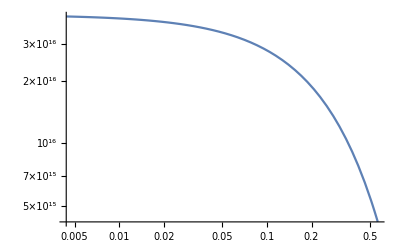

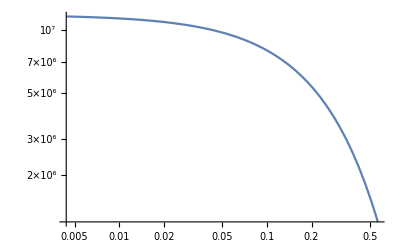

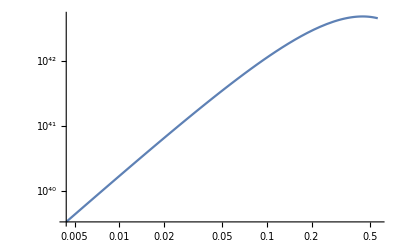

```mathematica
LogLogPlot[10^interrate1me[["f"]][β +Log10["me"/.CosmoParams[]]]/.CosmoParams[],{β,Log10[1/("Td")/.CosmoParams[]],Log10[1/("TR")/.CosmoParams[]]}]
LogLogPlot[nDR[10^-2,interrate1me[["mD"]]]10^interrate1me[["f"]][β +Log10["me"/.CosmoParams[]]]/.CosmoParams[],{β,Log10[1/("Td")/.CosmoParams[]],Log10[1/("TR")/.CosmoParams[]]}]
LogLogPlot[(10^interrate1me[["f"]][β +Log10["me"/.CosmoParams[]]])/H[β]/.CosmoParams[],{β,Log10[1/("Td")/.CosmoParams[]],Log10[1/("TR")/.CosmoParams[]]}]
```

```mathematica
nDR[10^-2,10^6]/.CosmoParams[]
```

1.42034×10^-10

```mathematica
Plot[NeffConstraint`ESMIntegral["me"/.CosmoParams[],"me"/.CosmoParams[],1,ξβ,CosmoParams[],1],{ξβ,1,10^6}]
```

$Aborted

```mathematica
?ESMIntegral
```

```mathematica
?NumIntegrand
```

```mathematica
NeffConstraint`NumIntegrand["me"/.CosmoParams[],"me"/.CosmoParams[],1,10^5,10^-5,CosmoParams[],0]
```

0.293113

```mathematica
Block[{l=1,Integrand,params=CosmoParams[],v1,v2,v3},
v1=Simplify[Integrate[Ett^l/(Ett+"Λ")^2 (("ms" + "ESMt")^2+("ms"+(Ett-"ESMt"))^2),Ett]];
	v2=Simplify[v1/."ms"->("m"^2+"mD"^2)/(2 "mD")];
	v3 =Simplify[Simplify[(v2/.Ett->(2 "mD")/(("ESMt"+"mD")^2/("ESMt"^2-"m"^2)-1))-(v2/.Ett->0)]];
Integrand=2/π ("α"^2 κ^2)/mDt (E^(-"β" "ESMt" + "β" "μ")/aH["β"]^l v3 /."μ"->"m" - 1/"β" Log["Qt"]/.{"Λ"->Λ["β"],"Qt"->Z1["β"]}/."ESMt"->1/"β" ξE + "m"/."β"->ξβ/"m"/.{"m"->mt,"mD"->mDt})/.params;
(*Print[v1];
Print[v2];*)
(*Print[Integrand];*)
Print[Integrand/.{"m"->"me"/.CosmoParams[],"mD"->"me"/.CosmoParams[],"κ"->1}/.CosmoParams[]]
]
```

(8.95453×10^31 ⅇ^(-((mt+(mt ξE)/ξβ) ξβ)/mt+(ξβ (mt-(mt Log[(7.10335×10^17)/(mt/ξβ)^(3/2)])/ξβ))/mt) mt κ^2 (-((mDt^2+mt^2)^2)/(2 mDt^2)+(2 (mt^2+mDt (mDt-2 (mt+(mt ξE)/ξβ)-(2.91415×10^-16 mt^2)/ξβ^2)) (-mt^2+(mt+(mt ξE)/ξβ)^2))/(mt^2+mDt (mDt+2 (mt+(mt ξE)/ξβ)))+(2 mDt^2)/((-1+(mDt+mt+(mt ξE)/ξβ)^2/(-mt^2+(mt+(mt ξE)/ξβ)^2))^2)-2 (mt+(mt ξE)/ξβ)^2-(2.12306×10^-32 mt^4)/ξβ^4+(1.45707×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(1.45707×10^-16 mt^2 (((mDt^2+mt^2)^2)/(2 mDt^2)+2 (mt+(mt ξE)/ξβ)^2+(2.12306×10^-32 mt^4)/ξβ^4-(1.45707×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(2.91415×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2))/(((2 mDt (-mt^2+(mt+(mt ξE)/ξβ)^2))/(mt^2+mDt (mDt+2 (mt+(mt ξE)/ξβ)))+(1.45707×10^-16 mt^2)/ξβ^2) ξβ^2)-(2.91415×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2+(((mDt^2+mt^2)^2)/(2 mDt^2)+2 (mt+(mt ξE)/ξβ)^2+(6.36919×10^-32 mt^4)/ξβ^4-(2.91415×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(5.82829×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2) Log[(2 mDt (-mt^2+(mt+(mt ξE)/ξβ)^2))/(mt^2+mDt (mDt+2 (mt+(mt ξE)/ξβ)))+(1.45707×10^-16 mt^2)/ξβ^2]-(((mDt^2+mt^2)^2)/(2 mDt^2)+2 (mt+(mt ξE)/ξβ)^2+(6.36919×10^-32 mt^4)/ξβ^4-(2.91415×10^-16 mt^2 (mDt^2+mt^2))/(mDt ξβ^2)+(5.82829×10^-16 mt^2 (mt+(mt ξE)/ξβ))/ξβ^2) Log[(1.45707×10^-16 mt^2)/ξβ^2]))/(mDt √(0.68+(2.4064×10^10 mt^4)/ξβ^4+(2.048×10^10 mt^3)/ξβ^3+(160000. mt^2)/ξβ^2) ξβ)

```mathematica
-2 ("ESMt"-"ms"+"Λ") Ett+Ett^2/2+("Λ" (2 ("ESMt")^2+2 ("ms")^2+2 "ESMt" "Λ"-2 "ms" "Λ"+("Λ")^2))/("Λ"+Ett)+(2 ("ESMt")^2+2 ("ms")^2+4 "ESMt" "Λ"-4 "ms" "Λ"+3 ("Λ")^2) Log["Λ"+Ett]/."ms"->("m"^2+"mD"^2)/(2 "mD")
Simplify[%]
```

-2 (ESMt-(m^2+mD^2)/(2 mD)+Λ) Ett+Ett^2/2+(Λ (2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+2 ESMt Λ-((m^2+mD^2) Λ)/mD+Λ^2))/(Λ+Ett)+(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[Λ+Ett]

((m^2+mD (-2 ESMt+mD-2 Λ)) Ett)/mD+Ett^2/2+(Λ (2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+2 ESMt Λ-((m^2+mD^2) Λ)/mD+Λ^2))/(Λ+Ett)+(2 ESMt^2+((m^2+mD^2)^2)/(2 mD^2)+4 ESMt Λ-(2 (m^2+mD^2) Λ)/mD+3 Λ^2) Log[Λ+Ett]

```mathematica
-1/(DΣ-1)+Simplify[-1/(DΣ-1)+DΣ/(DΣ-1)^2]
Simplify[(1-DΣ/(DΣ-1))^2]
```

1/(-1+DΣ)^2-1/(-1+DΣ)

1/(-1+DΣ)^2

### Yushin’s BOTE Calculation from CMB distortion

```mathematica
N[ϵ <= 1/α(T0/Mpl)^(1/2)/.{α->1/137,T0->10^-4 eV,Mpl->10^28 eV}]
```

ϵ≤1.37×10^-14

```mathematica
?nD0
nD0[0.01,10^9]/.CosmoParams[]
```

1.06712×10^-22

```mathematica
(*nD0=5 N["n0"/.CosmoParams[]]/100 eV^3(*dependent on aDM fraction*)*)

(α^2 ϵ^2 Mpl)/T0^4(eV^3 nD0[0.01,10^9]/.CosmoParams[] ) /.{α->1/137,T0->10^-4 eV,Mpl->10^28 eV}(*Γ/H using aDM fraction of order a percent*)
ϵ/.Solve[%==1,ϵ][[2]]
```

5.68554×10^17 ϵ^2

1.32622×10^-9

```mathematica
CosmoParams[]
```

{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}

this is wrong, I am misunderstanding something, There seems to be a factor of 10^-5 which I don’t know how to include

Yushin was also saying something about DOFs and entropy sharing

100 units of total energy stay in SM sector (some temperature, rad dominated), DS is in TE with SM so entropy split among DS and SM dofs => change of temperature, must be less than 10^{-5}. \Delta N_{eff} is from cosmo bounds etc.
Assumption here seems to be that the sectors equilibriate if they scatter at all.

What about at CMB times?

```mathematica
N[κ <= 1/α(TR/Mpl)^(1/2)/.{α->1/137,TR->0.25 eV,Mpl->10^28 eV}]
```

κ≤6.85×10^-13

```mathematica
"eVm"/.CosmoParams[]
```

2.×10^-7

```mathematica
N[κ <= 1/α(T0/Mpl)^(1/2)/.{α->1/137,T0->10^-4 eV,Mpl->10^28 eV}]
```

κ≤1.37×10^-14

```mathematica
(α^2 ϵ^2 Mpl)/T^4(eV^3 nD0[0.01,10^5](T/("T0"eV))^3/.CosmoParams[] ) /.{α->1/137,T->10^-1 eV,Mpl->10^28 eV}(*Γ/H using aDM fraction of order a percent*)
ϵ/.Solve[%==1,ϵ][[2]]
```

3.63875×10^17 ϵ^2

1.65777×10^-9

```mathematica
(α^2 ϵ^2 Mpl)/T^4(eV^3 nD0[0.01,10^5](T/("T0"eV))^3/.CosmoParams[] ) /.{g->0.1,α->1/137,T->10^-1 eV,Mpl->10^28 eV}(*Γ/H using aDM fraction of order a percent*)
ϵ/.Solve[%==1,ϵ][[2]]
```

3.63875×10^17 ϵ^2

1.65777×10^-9

```mathematica
g
```

g

```mathematica
CosmoParams[]
```

{Td→500000,ad→1/2000000000,Tdt→0.00025,T0→0.00025,aR→1/1100,TR→0.275,eVm→2.×10^-7,c→300000000,h→0.67,ρcrit→3.95032×10^-20,H0→1.51515×10^-33,n0→1.97516×10^-21,nd→1.58013×10^7,nr→2.62894×10^-12,me→500000,α→1/137,g→4,pth→4.46031,kF→3.88157×10^-7,EF→1.50666×10^-19,EFd→3.01332×10^-10,Degen→6.02664×10^-16,ρDM0→1.06712×10^-11}